```mathematica
(*simple pendulum*)
g=9.8; (*grav. constant*)
l=0.5; (*length of pendulum*)

θ0=20*π/180; (*20 degrees*)
ω0 = 0; (*starting from rest*)
(*ϕ=y;
t=x;*)
ode1={θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0};
sol=NDSolve[ode1,θ,{t,0,20}];
```

```mathematica
myplot1 = Plot[(180/Pi) θ[t]/.sol,{t,0,20},PlotStyle-> RGBColor[0,0,1],PlotRange-> All];
omega=√(g/l);
```

```mathematica
approx = (180/Pi) θ0 Cos[omega*t];
myplot2=Plot[approx,{t,0,20},PlotStyle-> RGBColor[1,0,0],PlotRange-> All];
```

Show::gcomb: Could not combine the graphics objects in {myplot1, GraphicsBox[List[List[List[], List[], List[Hue[0.67`, 0.6`, 0.6`], RGBColor[1, 0, 0], LineBox[List[Skeleton[1911]]]]]], List[Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, True], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[All, All]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[Automatic, Automatic]]]]}.

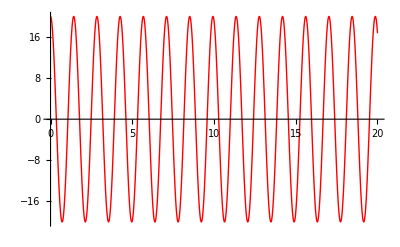
Show[{myplot1,-Graphics-}]

```mathematica
Show[{myplot1,myplot2}]
```

```mathematica
Manipulate[
g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]
```

```mathematica
g=9.8; (*grav. constant*)
vt=25
V=30
th=50 (Pi/180)
ode1={x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]}
ode2 ={y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2])}
sol=NDSolve[{ode1,ode2, x[0]==0,x'[0]==V Cos[th], y[0]==2, y'[0]==V Sin[th]},{x,y},{t,0,200}]
```

25

30

(5 π)/18

{x''[t]==-0.01568 x'[t] √(x'[t]^2+y'[t]^2)}

{y''[t]==-9.8 (1+1/625 y'[t] √(x'[t]^2+y'[t]^2))}

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

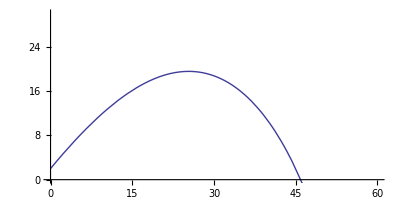

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol], {t,0,200},PlotRange-> {{0,60},{0,30}}]
```

```mathematica
Manipulate[
g=9.8;x0=0;y0=2;
Module[
{result = NDSolve[ode1,ode2, x[0]==x0,x'[0]==V Cos[th],y[0]==y0,y'[0]==V Sin[th]},{x,y},{t,0,tf}]},
ParametricPlot[{x[t],y[t]}/.result],{x0+V t Cos[th],y0+V  Sin[th t]-0.5 g t^2}},{t,0,tf},AxesLabel->{"x (m)","y (m)"},PlotRange->{{0,100},{0,50}},ImageSize->{500,300}]],
{{V,60,"initial velocity (m/s)"},0,200,Appearance->"Labeled"},{{th, Pi/6,"angle (rad)"},.1,Pi/2,Appearance->"Labeled"},
{{vt,35,"terminal velocity (m/s)"},0,100,Appearance->"Labeled"},{{tf,3,"time (s)"},0.1,100,Appearance->"Labeled"}]
```

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

RowReduce::inf: Input matrix contains an infinite entry.

NDSolve::ntdvmm: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system using a mass matrix method.

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000612245 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.